## Pre

```mathematica
SetDirectory@NotebookDirectory[]
```

/Users/leima/github/neuphysics/codebase/mma/dispersion-relation

```mathematica
Get["../../neupackage/mma/dispersion-relation.wl"]
```

```mathematica
?dispersion`*
```

```mathematica
colorf=Blend[{Blue,Red},#]&;
colorRainbow=ColorData["Rainbow"];
colorTemp=ColorData["Temperature"];
plotLegend[{min_,max_},n_,col_]:=Graphics[{{col[(#-1)/(n-1)],Rectangle[{0,#-1},{1,#}]},{Black,Text[NumberForm[Rescale[#,{1,n},{min,max}],{4,2}],{3,#-.5},{1,0}]}}&/@Range@n,Frame->True,FrameTicks->None,PlotRangePadding->.5]
```

```mathematica
pltcolors=ColorData[97,"ColorList"]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Prepare Spectrum

```mathematica
dataFakeNoCrossing={{-1,1.3},{-0.8,1.4},{-0.7,1.5},{-0.6,1.7},{-0.5,2},{0,2.5},{0.5,8},{1,6}}
dataFakeCrossing={{-1,-1.3},{-0.8,-1.0},{-0.7,-0.8},{-0.6,-0.3},{-0.5,-0.1},{0,0.5},{0.5,8},{1,6}}
```

{{-1,1.3},{-0.8,1.4},{-0.7,1.5},{-0.6,1.7},{-0.5,2},{0,2.5},{0.5,8},{1,6}}

{{-1,-1.3},{-0.8,-1.},{-0.7,-0.8},{-0.6,-0.3},{-0.5,-0.1},{0,0.5},{0.5,8},{1,6}}

```mathematica
spectFunCrossing[u_]=CoefficientList[
Fit[dataFakeCrossing,{1,u,u^2,u^3,u^4,u^5},u],
u].{1,u,u^2,u^3,u^4,u^5}
```

0.505427+5.64078 u+17.6868 u^2+13.9023 u^3-15.8373 u^4-15.8978 u^5

```mathematica
spectFunC2[u_]:=Sin[Pi u/1.2+Pi/6];
spectFunC3[u_]:=Sin[-Pi u/2+Pi/1.8];
spectFunC4[u_]:=-Sin[Pi u/1.2-Pi/6];
```

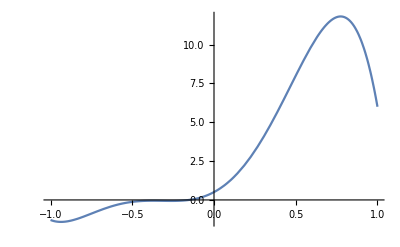

```mathematica
Plot[spectFunCrossing[u],{u,-1,1}]
```

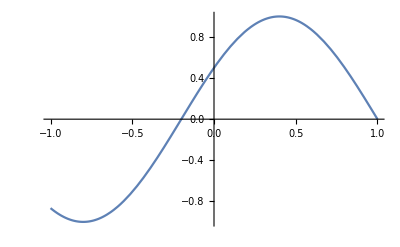

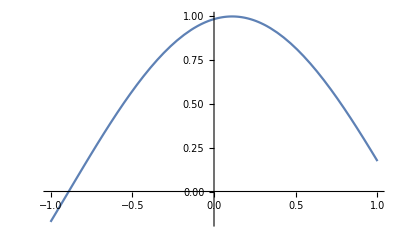

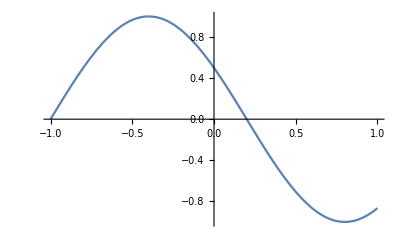

```mathematica
Plot[spectFunC2[u],{u,-1,1}]
Plot[spectFunC3[u],{u,-1,1}]
Plot[spectFunC4[u],{u,-1,1}]
```

```mathematica
spectFun[u_]=CoefficientList[
Fit[dataFakeCrossing,{1,u,u^2,u^3,u^4,u^5},u],
u].{1,u,u^2,u^3,u^4,u^5}
```

0.505427+5.64078 u+17.6868 u^2+13.9023 u^3-15.8373 u^4-15.8978 u^5

```mathematica
Plot[spectFun[u],{u,-1,1}]
```

-Graphics-

Define a test spectrum function which is identity.

```mathematica
spectFunUnity[u_]:=1
```

Calculate the DR

```mathematica
(IntFun0nFSpect[n,ct1,ct2,spectrumFun]+IntFun2nFSpect[n,ct1,ct2,spectrumFun]-2IntFun1nFSpect[n,ct1,ct2,spectrumFun])(IntFun0nFSpect[n,ct1,ct2,spectrumFun]+IntFun2nFSpect[n,ct1,ct2,spectrumFun]+2IntFun1nFSpect[n,ct1,ct2,spectrumFun])/.{n->0.9,ct1->-1,ct2->1,spectrumFun->spectFun}
```

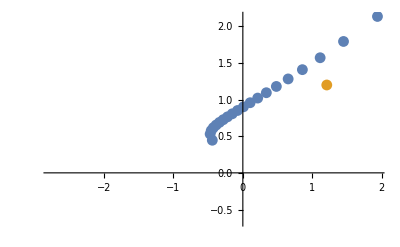

```mathematica
ListPlot[
{Table[
{n SpectrumOmegaNMAA[n,1,-1,spectFun],SpectrumOmegaNMAA[n,1,-1,spectFun]},
{n,-0.99,0.99,0.1}
],
Table[
{n SpectrumOmegaNMZA[n,1,-1,spectFun][[1]],SpectrumOmegaNMZA[n,1,-1,spectFun][[1]]},
{n,-0.99,1.99,1}
],
Table[
{n SpectrumOmegaNMZA[n,1,-1,spectFun][[2]],SpectrumOmegaNMZA[n,1,-1,spectFun][[2]]},
{n,-0.99,1.99,1}
]
}
]
```

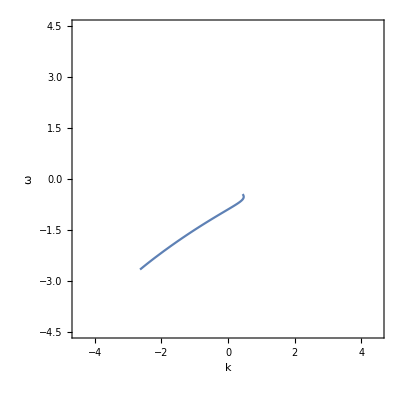

```mathematica
pltSpectMAA=ParametricPlot[
{n SpectrumOmegaNMAA[n,-1,1,spectFunCrossing],SpectrumOmegaNMAA[n,-1,1,spectFunCrossing]},
{n,-0.99,0.99},
PlotRange->{{-4.5,4.5},{-4.5,4.5}},
Frame->True,
FrameLabel->{"k","ω"}
]//Quiet
```

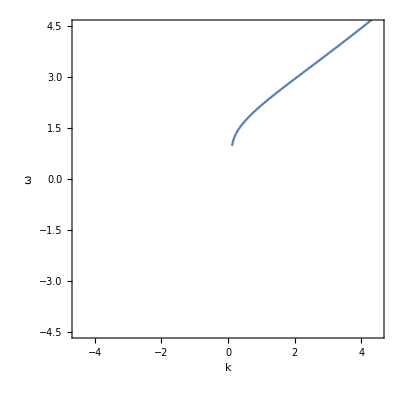

```mathematica
pltSpectMZAp=ParametricPlot[
{n SpectrumOmegaNMZA[n,-1,1,spectFunCrossing][[1]],SpectrumOmegaNMZA[n,-1,1,spectFunCrossing][[1]]},
{n,-0.99,0.99},
PlotRange->{{-4.5,4.5},{-4.5,4.5}},
Frame->True,
FrameLabel->{"k","ω"}
]//Quiet
```

```mathematica
pltSpectMZAm=ParametricPlot[
{n SpectrumOmegaNMZA[n,-1,1,spectFunCrossing][[2]],SpectrumOmegaNMZA[n,-1,1,spectFunCrossing][[2]]},
{n,-0.99,0.99},
PlotRange->{{-4.5,4.5},{-4.5,4.5}},
Frame->True,
FrameLabel->{"k","ω"}
]//Quiet
```

$Aborted

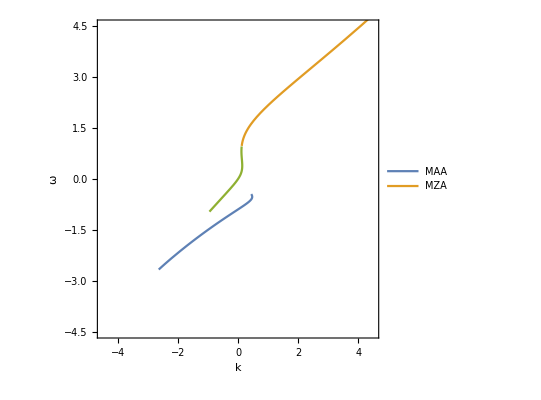

```mathematica
pltSpect=ParametricPlot[
{
{n SpectrumOmegaNMAA[n,-1,1,spectFunCrossing],SpectrumOmegaNMAA[n,-1,1,spectFunCrossing]},{n SpectrumOmegaNMZA[n,-1,1,spectFunCrossing][[1]],SpectrumOmegaNMZA[n,-1,1,spectFunCrossing][[1]]},
{n SpectrumOmegaNMZA[n,-1,1,spectFunCrossing][[2]],SpectrumOmegaNMZA[n,-1,1,spectFunCrossing][[2]]}
},
{n,-0.99,0.99},
PlotRange->{{-4.5,4.5},{-4.5,4.5}},
Frame->True,
FrameLabel->{"k","ω"},PlotLegends->Placed[{"MAA","MZA"},{Bottom,Right}]
]//Quiet
```

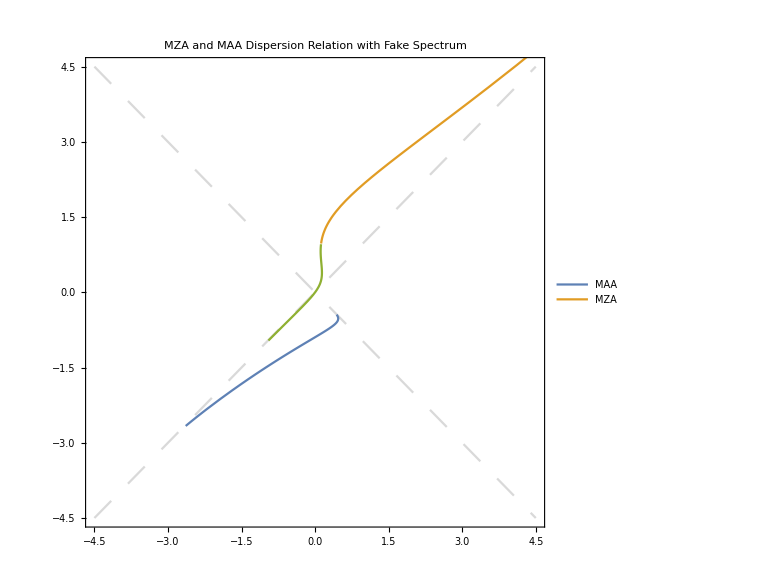

```mathematica
pltSpectGrids=Show[
Plot[{x,-x},{x,-7,7},PlotStyle->Directive[LightGray,Dashing[0.03]],Frame->True,ImageSize->Large,PlotRange->{{-4.5,4.5},{-4.5,4.5}},PlotLabel->"MZA and MAA Dispersion Relation with Fake Spectrum",AspectRatio->1],
pltSpect
]
```

## C2 spectrum

```mathematica
Table[
{n SpectrumOmegaNMZA[n,1,-1,spectFunC2][[2]],SpectrumOmegaNMZA[n,1,-1,spectFunC2][[2]]},
{n,-0.99,0.99,0.1}
]
```

{{-0.110191+0.847367 ⅈ,0.111304-0.855926 ⅈ},{-0.0458937+0.518806 ⅈ,0.051566-0.582928 ⅈ},{-0.017307+0.400631 ⅈ,0.0219076-0.507127 ⅈ},{-0.000907607+0.319393 ⅈ,0.00131537-0.462889 ⅈ},{0.00867232+0.255102 ⅈ,-0.0146988-0.432376 ⅈ},{0.0137221+0.200703 ⅈ,-0.0280043-0.409599 ⅈ},{0.0154373+0.152807 ⅈ,-0.0395828-0.391813 ⅈ},{0.0145076+0.109486 ⅈ,-0.0500262-0.377539 ⅈ},{0.0113486+0.0695199 ⅈ,-0.0597297-0.365894 ⅈ},{0.00620829+0.032069 ⅈ,-0.068981-0.356322 ⅈ},{-0.000780088-0.00348455 ⅈ,-0.0780088-0.348455 ⅈ},{-0.00957127-0.0376261 ⅈ,-0.0870115-0.342055 ⅈ},{-0.0201974-0.0707642 ⅈ,-0.0961783-0.336972 ⅈ},{-0.0327694-0.103271 ⅈ,-0.105708-0.333134 ⅈ},{-0.0474896-0.135522 ⅈ,-0.115828-0.330541 ⅈ},{-0.0646825-0.167937 ⅈ,-0.126829-0.329289 ⅈ},{-0.0848542-0.201064 ⅈ,-0.139105-0.329614 ⅈ},{-0.108815-0.235736 ⅈ,-0.153261-0.332022 ⅈ},{-0.137965-0.273518 ⅈ,-0.170327-0.337676 ⅈ},{-0.175135-0.318485 ⅈ,-0.192456-0.349983 ⅈ}}

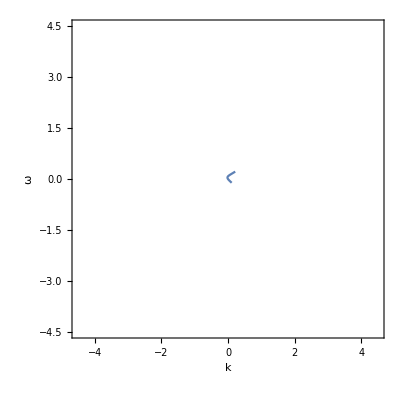

```mathematica
pltSpectC2MAA=ParametricPlot[
{n SpectrumOmegaNMAA[n,1,-1,spectFunC2],SpectrumOmegaNMAA[n,1,-1,spectFunC2]},
{n,-0.99,0.99},
PlotRange->{{-4.5,4.5},{-4.5,4.5}},
Frame->True,
FrameLabel->{"k","ω"},PlotStyle->pltcolors[[1]]
]//Quiet
```

```mathematica
pltSpectC2MZAp=ParametricPlot[
{n SpectrumOmegaNMZA[n,1,-1,spectFunC2][[1]],SpectrumOmegaNMZA[n,1,-1,spectFunC2][[1]]},
{n,-0.99,0.99},
PlotRange->{{-4.5,4.5},{-4.5,4.5}},
Frame->True,
FrameLabel->{"k","ω"},PlotStyle->pltcolors[[2]]
]//Quiet
```

-Graphics-

```mathematica
pltSpectC2MZAm=ParametricPlot[
{n SpectrumOmegaNMZA[n,1,-1,spectFunC2][[2]],SpectrumOmegaNMZA[n,1,-1,spectFunC2][[2]]},
{n,-0.99,0.99},
PlotRange->{{-4.5,4.5},{-4.5,4.5}},
Frame->True,
FrameLabel->{"k","ω"},PlotStyle->pltcolors[[3]]
]//Quiet
```

-Graphics-

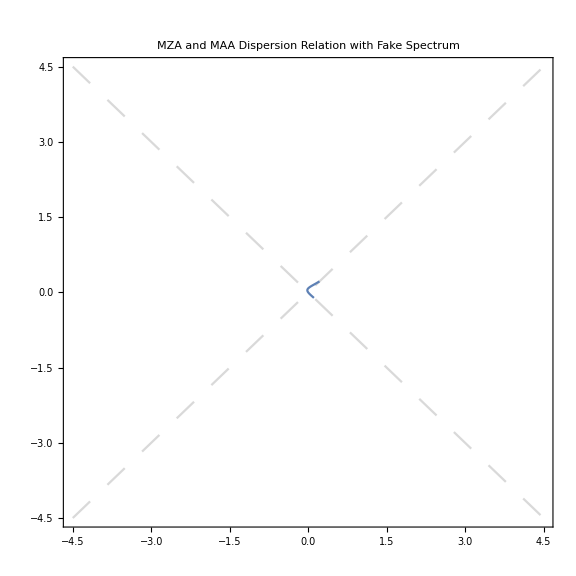

```mathematica
pltSpectC2Grids=Show[
Plot[{x,-x},{x,-7,7},PlotStyle->Directive[LightGray,Dashing[0.03]],Frame->True,ImageSize->Large,PlotRange->{{-4.5,4.5},{-4.5,4.5}},PlotLabel->"MZA and MAA Dispersion Relation with Fake Spectrum",AspectRatio->1],
pltSpectC2MAA,
pltSpectC2MZAp,
pltSpectC2MZAm
]
```

## C3 Spectrum

```mathematica
Table[
{n SpectrumOmegaNMZA[n,1,-1,spectFunC3][[2]],SpectrumOmegaNMZA[n,1,-1,spectFunC3][[2]]},
{n,-0.99,0.99,0.1}
]
```

{{0.550126,-0.555683},{0.574569,-0.645584},{0.504678,-0.638833},{0.434861,-0.630233},{0.367704,-0.623226},{0.302917,-0.618197},{0.239889,-0.615099},{0.178013,-0.613838},{0.116727,-0.614353},{0.0554973,-0.616637},{-0.00620741,-0.620741},{-0.0689467,-0.626788},{-0.133347,-0.634986},{-0.200155,-0.645662},{-0.270319,-0.659314},{-0.345127,-0.67672},{-0.426482,-0.69915},{-0.517497,-0.728869},{-0.624175,-0.770587},{-0.762411,-0.837815}}

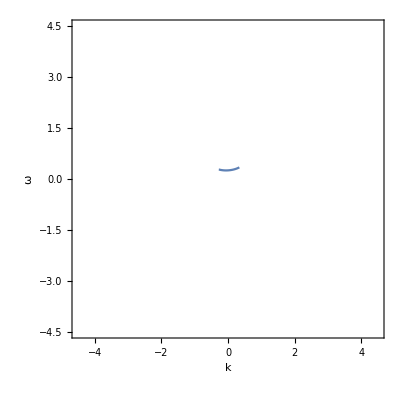

```mathematica
pltSpectC3MAA=ParametricPlot[
{n SpectrumOmegaNMAA[n,1,-1,spectFunC3],SpectrumOmegaNMAA[n,1,-1,spectFunC3]},
{n,-0.99,0.99},
PlotRange->{{-4.5,4.5},{-4.5,4.5}},
Frame->True,
FrameLabel->{"k","ω"},PlotStyle->pltcolors[[1]]
]//Quiet
```

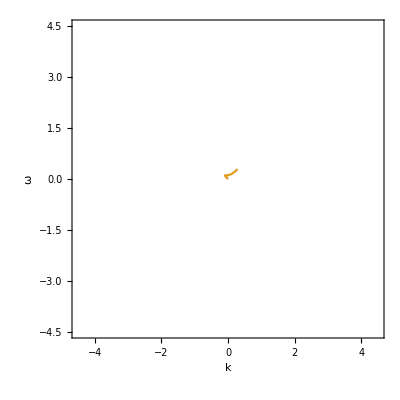

```mathematica
pltSpectC3MZAp=ParametricPlot[
{n SpectrumOmegaNMZA[n,1,-1,spectFunC3][[1]],SpectrumOmegaNMZA[n,1,-1,spectFunC3][[1]]},
{n,-0.99,0.99},
PlotRange->{{-4.5,4.5},{-4.5,4.5}},
Frame->True,
FrameLabel->{"k","ω"},PlotStyle->pltcolors[[2]]
]//Quiet
```

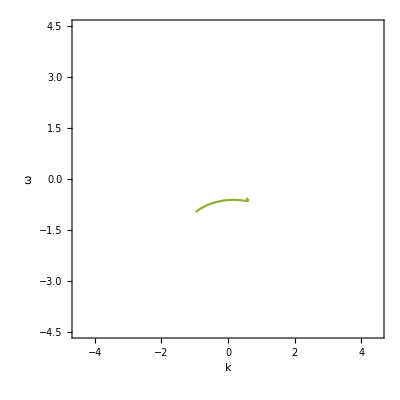

```mathematica
pltSpectC3MZAm=ParametricPlot[
{n SpectrumOmegaNMZA[n,1,-1,spectFunC3][[2]],SpectrumOmegaNMZA[n,1,-1,spectFunC3][[2]]},
{n,-0.99,0.99},
PlotRange->{{-4.5,4.5},{-4.5,4.5}},
Frame->True,
FrameLabel->{"k","ω"},PlotStyle->pltcolors[[3]]
]//Quiet
```

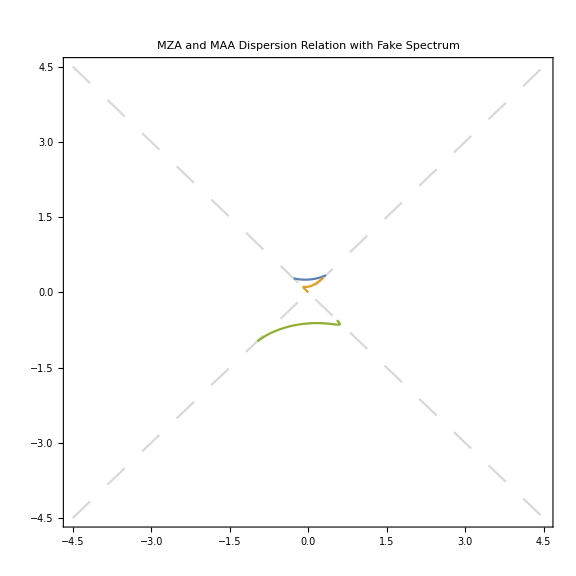

```mathematica
pltSpectC3Grids=Show[
Plot[{x,-x},{x,-7,7},PlotStyle->Directive[LightGray,Dashing[0.03]],Frame->True,ImageSize->Large,PlotRange->{{-4.5,4.5},{-4.5,4.5}},PlotLabel->"MZA and MAA Dispersion Relation with Fake Spectrum",AspectRatio->1],
pltSpectC3MAA,
pltSpectC3MZAp,
pltSpectC3MZAm
]
```

## C4 Spectrum

```mathematica
Table[
{n SpectrumOmegaNMZA[n,1,-1,spectFunC4][[2]],SpectrumOmegaNMZA[n,1,-1,spectFunC4][[2]]},
{n,-0.99,0.99,0.1}
]
```

{{0.21595+0.373801 ⅈ,-0.218132-0.377577 ⅈ},{0.166818+0.308481 ⅈ,-0.187436-0.346608 ⅈ},{0.131618+0.265585 ⅈ,-0.166605-0.336184 ⅈ},{0.103665+0.22862 ⅈ,-0.150239-0.331333 ⅈ},{0.0805486+0.194348 ⅈ,-0.136523-0.329404 ⅈ},{0.0610252+0.161418 ⅈ,-0.124541-0.329424 ⅈ},{0.0443603+0.129073 ⅈ,-0.113744-0.330957 ⅈ},{0.0300911+0.0968029 ⅈ,-0.103762-0.333803 ⅈ},{0.0179213+0.0641987 ⅈ,-0.0943226-0.337888 ⅈ},{0.00766835+0.0308904 ⅈ,-0.0852039-0.343226 ⅈ},{-0.000762114-0.00349905 ⅈ,-0.0762114-0.349905 ⅈ},{-0.00738709-0.0393899 ⅈ,-0.0671553-0.35809 ⅈ},{-0.012145-0.077289 ⅈ,-0.0578333-0.368043 ⅈ},{-0.0148823-0.11785 ⅈ,-0.0480074-0.380161 ⅈ},{-0.015323-0.161972 ⅈ,-0.0373732-0.395053 ⅈ},{-0.0130077-0.210983 ⅈ,-0.0255053-0.413692 ⅈ},{-0.00717039-0.267019 ⅈ,-0.0117547-0.437735 ⅈ},{0.00353666-0.333943 ⅈ,0.00498121-0.470342 ⅈ},{0.021771-0.420165 ⅈ,0.0268778-0.518723 ⅈ},{0.0541856-0.552065 ⅈ,0.0595446-0.606665 ⅈ}}

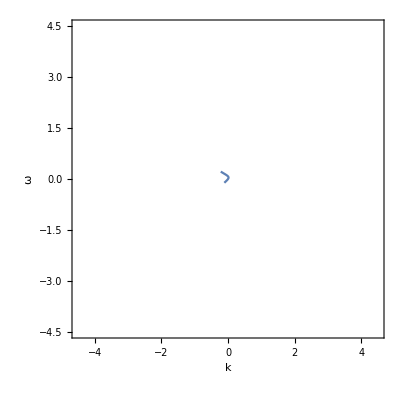

```mathematica
pltSpectC4MAA=ParametricPlot[
{n SpectrumOmegaNMAA[n,1,-1,spectFunC4],SpectrumOmegaNMAA[n,1,-1,spectFunC4]},
{n,-0.99,0.99},
PlotRange->{{-4.5,4.5},{-4.5,4.5}},
Frame->True,
FrameLabel->{"k","ω"},PlotStyle->pltcolors[[1]]
]//Quiet
```

```mathematica
pltSpectC4MZAp=ParametricPlot[
{n SpectrumOmegaNMZA[n,1,-1,spectFunC4][[1]],SpectrumOmegaNMZA[n,1,-1,spectFunC4][[1]]},
{n,-0.99,0.99},
PlotRange->{{-4.5,4.5},{-4.5,4.5}},
Frame->True,
FrameLabel->{"k","ω"},PlotStyle->pltcolors[[2]]
]//Quiet
```

-Graphics-

```mathematica
pltSpectC4MZAm=ParametricPlot[
{n SpectrumOmegaNMZA[n,1,-1,spectFunC4][[2]],SpectrumOmegaNMZA[n,1,-1,spectFunC4][[2]]},
{n,-0.99,0.99},
PlotRange->{{-4.5,4.5},{-4.5,4.5}},
Frame->True,
FrameLabel->{"k","ω"},PlotStyle->pltcolors[[3]]
]//Quiet
```

-Graphics-

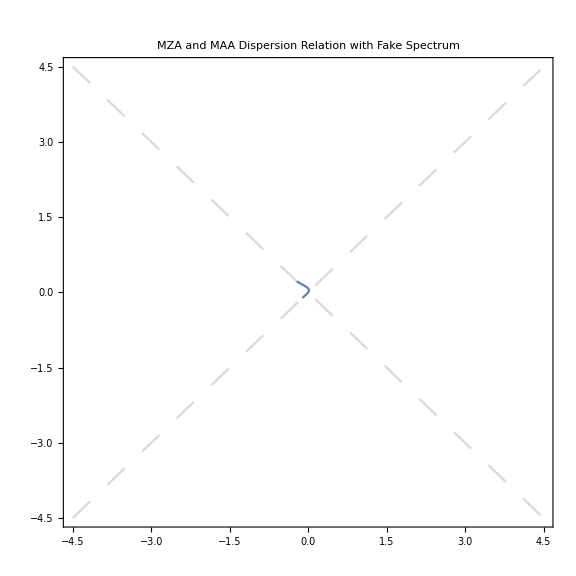

```mathematica
pltSpectC4Grids=Show[
Plot[{x,-x},{x,-7,7},PlotStyle->Directive[LightGray,Dashing[0.03]],Frame->True,ImageSize->Large,PlotRange->{{-4.5,4.5},{-4.5,4.5}},PlotLabel->"MZA and MAA Dispersion Relation with Fake Spectrum",AspectRatio->1],
pltSpectC4MAA,
pltSpectC4MZAp,
pltSpectC4MZAm
]
```

Linear Stability Analysis

### Generate Map

#### Grab data and validate

```mathematica
maalsadata={#[[1]],#[[2]],Abs@#[[3]]}&/@Import["maalsadata-fakedata.csv"];
mzaplsadata=Import["mzaplsadata-fakedata.csv"];
mzamlsadata=Import["mzamlsadata-fakedata.csv"];
maarealklsadata=Import["maarealklsadata-fakedata.csv"];
```

```mathematica
Flatten@#&/@maalsadata
```

```mathematica
maalsadataClean=Select[Flatten@#&/@maalsadata,(-4.5<#[[1]]<4.5)&&(-4.5<#[[2]]<4.5)&&(-500<#[[3]]<500)&];
mzaplsadataClean=Select[Flatten@#&/@mzaplsadata,(-4.5<#[[1]]<4.5)&&(-4.5<#[[2]]<4.5)&&(-500<#[[3]]<500)&];
mzamlsadataClean=Select[Flatten@#&/@mzamlsadata,(-4.5<#[[1]]<4.5)&&(-4.5<#[[2]]<4.5)&&(-500<#[[3]]<500)&];
maarealklsadataClean=Select[Flatten@#&/@maarealklsadata,(-4.5<#[[1]]<4.5)&&(-4.5<#[[2]]<4.5)&&(-500<#[[3]]<500)&];
```

```mathematica
maalsadata
```

```mathematica
mzamlsadataClean
mzaplsadataClean
```

```mathematica
SpectrumOmegaKMAAEqnLHS[#[[1]],0,#[[2]],#[[3]],spectFun]&/@maalsadataClean//Quiet
```

$Aborted

```mathematica
SpectrumOmegaKMAAEqnLHS[#[[1]],0,#[[2]],#[[3]],spectFun]&/@{Last@maalsadataClean}
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {0.0234064}. NIntegrate obtained -0.441553 - 1.2808×10^-16\ ⅈ and 0.278924 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {0.0234064}. NIntegrate obtained -0.0815534 - 2.56311×10^-19\ ⅈ and 0.00014022 for the integral and error estimates.

{{3.15026×10^-15,-3.19559×10^-17}}

```mathematica
Part[maalsadataClean,
Flatten@Position[
Chop[
SpectrumOmegaKMAAEqnLHS[#[[1]],0,#[[2]],#[[3]],spectFun]&/@(Flatten@#&/@maalsadataClean),
10^(-5)
]//Quiet,
{0,0}]
];
```

```mathematica
maalsadataCleanTestData=Select[Flatten@#&/@maalsadata,-3.2<#[[2]]<-3&]
```

{{-3.149,-3.18949,3.66698×10^-14},{-3.139,-3.17728,3.73609×10^-20},{-3.129,-3.16715,3.55892×10^-13},{-3.119,-3.16585,4.22388×10^-13},{-3.109,-3.14408,5.40777×10^-15},{-3.099,-3.13351,1.29166×10^-19},{-3.089,-3.12247,1.79765×10^-13},{-3.079,-3.11103,3.63605×10^-17},{-3.069,-3.10007,2.67746×10^-19},{-3.059,-3.0888,1.23952×10^-18},{-3.049,-3.07772,1.19705×10^-15},{-3.039,-3.06617,6.20775×10^-15},{-3.029,-3.05469,5.68904×10^-16},{-3.019,-3.04384,2.96478×10^-14},{-3.009,-3.03341,2.07802×10^-18},{-2.999,-3.02104,7.45421×10^-17},{-2.989,-3.01023,4.14083×10^-15}}

```mathematica
SpectrumOmegaKMAAEqnLHS[-3.1489999999999996,0,-3.1894863303523797,3.666978300135195*^-14,spectFun]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {0.987249217158542}. NIntegrate obtained 62.3743  - 2.38755×10^-8\ ⅈ and 33.027 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {0.987249217158542}. NIntegrate obtained 49.7783  - 2.3272×10^-8\ ⅈ and 32.1939 for the integral and error estimates.

{-4.43734×10^-9,-1.50872×10^-10}

```mathematica
{#,
Chop[
SpectrumOmegaKMAAEqnLHS[#[[1]],0,#[[2]],#[[3]],spectFun],
10^(-5)]}&/@(maalsadataCleanTestData)
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {0.987249217158542}. NIntegrate obtained 62.3743  - 2.38755×10^-8\ ⅈ and 33.027 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {0.987249217158542}. NIntegrate obtained 49.7783  - 2.3272×10^-8\ ⅈ and 32.1939 for the integral and error estimates.

{{{-3.149,-3.18949,3.66698×10^-14},{0,0}}}

#### Make Plot

```mathematica
Show[
Graphics[
{Point[-{#[[2]],#[[1]]}&/@maalsadataClean,VertexColors->colorf/@Rescale@(#[[3]]&/@maalsadataClean)],Inset[plotLegend[{Min@#,Max@#}&@(#[[3]]&/@maalsadataClean),20,colorf],Scaled[{1,1/2}],ImageScaled[{-0.1,1/2}],Scaled[{1/4,0.9}]]
},Axes->True,Frame->True,ImageSize->Large,FrameLabel->{"k.real","omega"},PlotLabel->"k.imag for different omega vs k.real: MAA",
ImageSize->Large,
ImagePadding->{{20, 90}, {20, 20}},
AspectRatio->1,PlotRange->{{-4.5,4.5},{-4.5,4.5}}
],
Show[
pltSpectGrids
],FrameLabel->{"omega","k"}
]
```

-Graphics-

```mathematica
Show[
Graphics[
{Point[-{#[[3]],#[[1]]}&/@maarealklsadataClean,VertexColors->colorf/@Rescale@(#[[2]]&/@maarealklsadataClean)],Inset[plotLegend[{Min@#,Max@#}&@(#[[2]]&/@maarealklsadataClean),20,colorf],Scaled[{1,1/2}],ImageScaled[{-0.1,1/2}],Scaled[{1/4,0.9}]]
},Axes->True,Frame->True,ImageSize->Large,FrameLabel->{"k.real","omega"},PlotLabel->"k.imag for different omega vs k.real: MAA",
ImageSize->Large,
ImagePadding->{{20, 90}, {20, 20}},
AspectRatio->1,PlotRange->{{-4.5,4.5},{-4.5,4.5}}
],
Show[
pltSpectGrids
],FrameLabel->{"omega","k"}
]
```

-Graphics-

```mathematica
Part[mzaplsadata,
Flatten@Position[
Chop[
SpectrumOmegaKMZApEqnLHS[#[[1]],0,#[[2]],#[[3]],spectFun]&/@(Flatten@#&/@mzaplsadata),
10^(-5)
]//Quiet,
{0,0}]
]
```

```mathematica
Show[
Graphics[
{Point[{#[[2]],#[[1]]}&/@mzaplsadataClean,VertexColors->colorf/@Rescale@(Abs[#[[3]]]&/@mzaplsadataClean)],Inset[plotLegend[{Min@#,Max@#}&@(Abs@#[[3]]&/@mzaplsadataClean),20,colorf],Scaled[{1,1/2}],ImageScaled[{-0.1,1/2}],Scaled[{1/4,0.9}]]
},Axes->True,Frame->True,ImageSize->Large,FrameLabel->{"k.real","omega"},PlotLabel->"k.imag for different omega vs k.real: MZA+",
ImageSize->Large,
ImagePadding->{{20, 90}, {20, 20}},
AspectRatio->1,PlotRange->{{-4.5,4.5},{-4.5,4.5}}
],
Show[
pltSpectGrids
]
]
```

-Graphics-

```mathematica
Show[
Graphics[
{Point[{#[[2]],#[[1]]}&/@mzamlsadataClean,VertexColors->colorf/@Rescale@(#[[3]]&/@mzamlsadataClean)],Inset[plotLegend[{Min@#,Max@#}&@(#[[3]]&/@mzamlsadataClean),20,colorf],Scaled[{1,1/2}],ImageScaled[{-0.1,1/2}],Scaled[{1/4,0.9}]]
},Axes->True,Frame->True,ImageSize->Large,FrameLabel->{"k.real","omega"},PlotLabel->"k.imag for different omega vs k.real: MZA-",
ImageSize->Large,
ImagePadding->{{20, 90}, {20, 20}},
AspectRatio->1,PlotRange->{{-4.5,4.5},{-4.5,4.5}}
],
Show[
pltSpectGrids
]
]
```

-Graphics-